```mathematica
PSF[x_,y_,z_]:=√(1/π)ⅈ/(z+ⅈ)Exp[-ⅈ  (x^2+y^2)/(2 (z+ⅈ ))-ⅈ k zR z];
PSFc[x_,y_,z_]:=√(1/π)-ⅈ/(z-ⅈ)Exp[ⅈ  (x^2+y^2)/(2 (z-ⅈ ))+ⅈ k zR z];
assumpt={Element[x,Reals],Element[y,Reals],Element[z,Reals],p1>0,s1>0, t1>0,p2>0,s2>0,t2>0, k>0,zR>0};
psi[1][x_,y_]:=PSF[x+s1,y+ t1,p1];
psi[2][x_,y_]:=PSF[x+s2,y+ t2,p2];
psi[3][x_,y_]:=D[psi[1][x,y],s1]//Evaluate;
psi[4][x_,y_]:=D[psi[2][x,y],s2]//Evaluate;
psi[5][x_,y_]:=D[psi[1][x,y],t1]//Evaluate;
psi[6][x_,y_]:=D[psi[2][x,y],t2]//Evaluate;
psi[7][x_,y_]:=D[psi[1][x,y],p1]//Evaluate;
psi[8][x_,y_]:=D[psi[2][x,y],p2]//Evaluate;

psic[1][x_,y_]:=PSFc[x+s1,y+t1,p1];
psic[2][x_,y_]:=PSFc[x+s2,y+t2,p2];
psic[3][x_,y_]:=D[psic[1][x,y],s1]//Evaluate;
psic[4][x_,y_]:=D[psic[2][x,y],s2]//Evaluate;
psic[5][x_,y_]:=D[psic[1][x,y],t1]//Evaluate;
psic[6][x_,y_]:=D[psic[2][x,y],t2]//Evaluate;
psic[7][x_,y_]:=D[psic[1][x,y],p1]//Evaluate;
psic[8][x_,y_]:=D[psic[2][x,y],p2]//Evaluate;

coords:={s1->1.3,s2-> 0.7, t1->0.93, t2->1.17,p1->0.23,p2->0.0654, k->2, zR->1};
g[i_,j_]:=2π Simplify[FourierTransform[Simplify[psic[i][x,y]psi[j][x,y],assumpt],{x,y},{a,b},Assumptions->assumpt],assumpt]/.{a->0,b->0};
LPsolver[a_,d_,G_]:=Module[{A=Simplify[a.G],B=Simplify[G.a],l,elements=Table[If[Min[i,j]≥3,0,l[i,j]],{i,1,3},{j,1,3}],vars,eq1,sol},vars=DeleteCases[Flatten[elements],0];eq1=Flatten[A.elements+elements.B==2d];sol=Solve[eq1,vars];(elements/.sol)[[1]]]
```

```mathematica
(*G=Table[g[i,j],{i,1,8},{j,1,8}];*)
```

```mathematica
G = {{1,(2 ⅈ ⅇ^((ⅈ (s1^2-2 s1 s2+s2^2+t1^2-2 t1 t2+t2^2-4 ⅈ k p1 zR+2 k p1^2 zR+4 ⅈ k p2 zR-4 k p1 p2 zR+2 k p2^2 zR))/(2 (-2 ⅈ+p1-p2))))/(2 ⅈ-p1+p2),0,-(2 ⅇ^((ⅈ (s1^2-2 s1 s2+s2^2+t1^2-2 t1 t2+t2^2-4 ⅈ k p1 zR+2 k p1^2 zR+4 ⅈ k p2 zR-4 k p1 p2 zR+2 k p2^2 zR))/(2 (-2 ⅈ+p1-p2))) (s1-s2))/(2 ⅈ-p1+p2)^2,0,-(2 ⅇ^((ⅈ (s1^2-2 s1 s2+s2^2+t1^2-2 t1 t2+t2^2-4 ⅈ k p1 zR+2 k p1^2 zR+4 ⅈ k p2 zR-4 k p1 p2 zR+2 k p2^2 zR))/(2 (-2 ⅈ+p1-p2))) (t1-t2))/(2 ⅈ-p1+p2)^2,-1/8 ⅈ (-4+8 k zR),1/(-2 ⅈ+p1-p2)^3 ⅇ^((ⅈ (s1^2-2 s1 s2+s2^2+t1^2-2 t1 t2+t2^2-4 ⅈ k p1 zR+2 k p1^2 zR+4 ⅈ k p2 zR-4 k p1 p2 zR+2 k p2^2 zR))/(2 (-2 ⅈ+p1-p2))) (-4-2 ⅈ p1+2 ⅈ p2+s1^2-2 s1 s2+s2^2+t1^2-2 t1 t2+t2^2+8 k zR+8 ⅈ k p1 zR-2 k p1^2 zR-8 ⅈ k p2 zR+4 k p1 p2 zR-2 k p2^2 zR)},{(2 ⅈ ⅇ^(-(ⅈ (s1^2-2 s1 s2+s2^2+t1^2-2 t1 t2+t2^2+4 ⅈ k p1 zR+2 k p1^2 zR-4 ⅈ k p2 zR-4 k p1 p2 zR+2 k p2^2 zR))/(2 (2 ⅈ+p1-p2))))/(2 ⅈ+p1-p2),1,-(2 ⅇ^(-(ⅈ (s1^2-2 s1 s2+s2^2+t1^2-2 t1 t2+t2^2+4 ⅈ k p1 zR+2 k p1^2 zR-4 ⅈ k p2 zR-4 k p1 p2 zR+2 k p2^2 zR))/(2 (2 ⅈ+p1-p2))) (-s1+s2))/(2 ⅈ+p1-p2)^2,0,-(2 ⅇ^(-(ⅈ (s1^2-2 s1 s2+s2^2+t1^2-2 t1 t2+t2^2+4 ⅈ k p1 zR+2 k p1^2 zR-4 ⅈ k p2 zR-4 k p1 p2 zR+2 k p2^2 zR))/(2 (2 ⅈ+p1-p2))) (-t1+t2))/(2 ⅈ+p1-p2)^2,0,1/(2 ⅈ+p1-p2)^3 ⅇ^(-(ⅈ (s1^2-2 s1 s2+s2^2+t1^2-2 t1 t2+t2^2+4 ⅈ k p1 zR+2 k p1^2 zR-4 ⅈ k p2 zR-4 k p1 p2 zR+2 k p2^2 zR))/(2 (2 ⅈ+p1-p2))) (4-2 ⅈ p1+2 ⅈ p2-s1^2+2 s1 s2-s2^2-t1^2+2 t1 t2-t2^2-8 k zR+8 ⅈ k p1 zR+2 k p1^2 zR-8 ⅈ k p2 zR-4 k p1 p2 zR+2 k p2^2 zR),-1/8 ⅈ (-4+8 k zR)},{0,(2 ⅇ^((ⅈ (s1^2-2 s1 s2+s2^2+t1^2-2 t1 t2+t2^2-4 ⅈ k p1 zR+2 k p1^2 zR+4 ⅈ k p2 zR-4 k p1 p2 zR+2 k p2^2 zR))/(2 (-2 ⅈ+p1-p2))) (s1-s2))/(2 ⅈ-p1+p2)^2,1/2,1/(2 ⅈ-p1+p2)^3 2 ⅈ ⅇ^((ⅈ (s1^2-2 s1 s2+s2^2+t1^2-2 t1 t2+t2^2-4 ⅈ k p1 zR+2 k p1^2 zR+4 ⅈ k p2 zR-4 k p1 p2 zR+2 k p2^2 zR))/(2 (-2 ⅈ+p1-p2))) (-2-ⅈ p1+ⅈ p2+s1^2-2 s1 s2+s2^2),0,(2 ⅈ ⅇ^((ⅈ (s1^2-2 s1 s2+s2^2+t1^2-2 t1 t2+t2^2-4 ⅈ k p1 zR+2 k p1^2 zR+4 ⅈ k p2 zR-4 k p1 p2 zR+2 k p2^2 zR))/(2 (-2 ⅈ+p1-p2))) (s1-s2) (t1-t2))/(2 ⅈ-p1+p2)^3,0,-1/((ⅈ+p2)^3 (2 ⅈ-p1+p2)^4)ⅇ^((ⅈ (s1^2-2 s1 s2+s2^2+t1^2-2 t1 t2+t2^2-4 ⅈ k p1 zR+2 k p1^2 zR+4 ⅈ k p2 zR-4 k p1 p2 zR+2 k p2^2 zR))/(2 (-2 ⅈ+p1-p2))) (-1+ⅈ p2)^3 (s1-s2) (-8+4 ⅈ p2+s1^2-2 s1 s2+s2^2+t1^2-2 t1 t2+t2^2+8 k zR-2 k p1^2 zR-8 ⅈ k p2 zR-2 k p2^2 zR+4 p1 (-ⅈ+k (2 ⅈ+p2) zR))},{(2 ⅇ^(-(ⅈ (s1^2-2 s1 s2+s2^2+t1^2-2 t1 t2+t2^2+4 ⅈ k p1 zR+2 k p1^2 zR-4 ⅈ k p2 zR-4 k p1 p2 zR+2 k p2^2 zR))/(2 (2 ⅈ+p1-p2))) (-s1+s2))/(2 ⅈ+p1-p2)^2,0,1/(2 ⅈ+p1-p2)^3 2 ⅈ ⅇ^(-(ⅈ (s1^2-2 s1 s2+s2^2+t1^2-2 t1 t2+t2^2+4 ⅈ k p1 zR+2 k p1^2 zR-4 ⅈ k p2 zR-4 k p1 p2 zR+2 k p2^2 zR))/(2 (2 ⅈ+p1-p2))) (-2+ⅈ p1-ⅈ p2+s1^2-2 s1 s2+s2^2),1/2,1/(2 ⅈ+p1-p2)^3 2 ⅈ ⅇ^(-(ⅈ (s1^2-2 s1 s2+s2^2+t1^2-2 t1 t2+t2^2+4 ⅈ k p1 zR+2 k p1^2 zR-4 ⅈ k p2 zR-4 k p1 p2 zR+2 k p2^2 zR))/(2 (2 ⅈ+p1-p2))) (-s1+s2) (-t1+t2),0,-1/(2 ⅈ+p1-p2)^4 ⅈ ⅇ^(-(ⅈ (s1^2-2 s1 s2+s2^2+t1^2-2 t1 t2+t2^2+4 ⅈ k p1 zR+2 k p1^2 zR-4 ⅈ k p2 zR-4 k p1 p2 zR+2 k p2^2 zR))/(2 (2 ⅈ+p1-p2))) (s1-s2) (-8-4 ⅈ p2+s1^2-2 s1 s2+s2^2+t1^2-2 t1 t2+t2^2+8 k zR-2 k p1^2 zR+8 ⅈ k p2 zR-2 k p2^2 zR+4 p1 (ⅈ+k (-2 ⅈ+p2) zR)),0},{0,(2 ⅇ^((ⅈ (s1^2-2 s1 s2+s2^2+t1^2-2 t1 t2+t2^2-4 ⅈ k p1 zR+2 k p1^2 zR+4 ⅈ k p2 zR-4 k p1 p2 zR+2 k p2^2 zR))/(2 (-2 ⅈ+p1-p2))) (t1-t2))/(2 ⅈ-p1+p2)^2,0,(2 ⅈ ⅇ^((ⅈ (s1^2-2 s1 s2+s2^2+t1^2-2 t1 t2+t2^2-4 ⅈ k p1 zR+2 k p1^2 zR+4 ⅈ k p2 zR-4 k p1 p2 zR+2 k p2^2 zR))/(2 (-2 ⅈ+p1-p2))) (s1-s2) (t1-t2))/(2 ⅈ-p1+p2)^3,1/2,1/(2 ⅈ-p1+p2)^3 2 ⅈ ⅇ^((ⅈ (s1^2-2 s1 s2+s2^2+t1^2-2 t1 t2+t2^2-4 ⅈ k p1 zR+2 k p1^2 zR+4 ⅈ k p2 zR-4 k p1 p2 zR+2 k p2^2 zR))/(2 (-2 ⅈ+p1-p2))) (-2-ⅈ p1+ⅈ p2+t1^2-2 t1 t2+t2^2),0,1/(2 ⅈ-p1+p2)^4 ⅈ ⅇ^((ⅈ (s1^2-2 s1 s2+s2^2+t1^2-2 t1 t2+t2^2-4 ⅈ k p1 zR+2 k p1^2 zR+4 ⅈ k p2 zR-4 k p1 p2 zR+2 k p2^2 zR))/(2 (-2 ⅈ+p1-p2))) (t1-t2) (-8+s1^2-2 s1 s2+s2^2+t1^2-2 t1 t2+t2^2+8 k zR-2 k p1^2 zR-2 k p2^2 zR-4 ⅈ p2 (-1+2 k zR)+4 p1 (-ⅈ+k (2 ⅈ+p2) zR))},{(2 ⅇ^(-(ⅈ (s1^2-2 s1 s2+s2^2+t1^2-2 t1 t2+t2^2+4 ⅈ k p1 zR+2 k p1^2 zR-4 ⅈ k p2 zR-4 k p1 p2 zR+2 k p2^2 zR))/(2 (2 ⅈ+p1-p2))) (-t1+t2))/(2 ⅈ+p1-p2)^2,0,1/(2 ⅈ+p1-p2)^3 2 ⅈ ⅇ^(-(ⅈ (s1^2-2 s1 s2+s2^2+t1^2-2 t1 t2+t2^2+4 ⅈ k p1 zR+2 k p1^2 zR-4 ⅈ k p2 zR-4 k p1 p2 zR+2 k p2^2 zR))/(2 (2 ⅈ+p1-p2))) (-s1+s2) (-t1+t2),0,1/(2 ⅈ+p1-p2)^3 2 ⅈ ⅇ^(-(ⅈ (s1^2-2 s1 s2+s2^2+t1^2-2 t1 t2+t2^2+4 ⅈ k p1 zR+2 k p1^2 zR-4 ⅈ k p2 zR-4 k p1 p2 zR+2 k p2^2 zR))/(2 (2 ⅈ+p1-p2))) (-2+ⅈ p1-ⅈ p2+t1^2-2 t1 t2+t2^2),1/2,-1/(2 ⅈ+p1-p2)^4 ⅈ ⅇ^(-(ⅈ (s1^2-2 s1 s2+s2^2+t1^2-2 t1 t2+t2^2+4 ⅈ k p1 zR+2 k p1^2 zR-4 ⅈ k p2 zR-4 k p1 p2 zR+2 k p2^2 zR))/(2 (2 ⅈ+p1-p2))) (t1-t2) (-8+s1^2-2 s1 s2+s2^2+t1^2-2 t1 t2+t2^2+8 k zR-2 k p1^2 zR-2 k p2^2 zR+4 ⅈ p2 (-1+2 k zR)+4 p1 (ⅈ+k (-2 ⅈ+p2) zR)),0},{1/8 ⅈ (-4+8 k zR),-1/(-2 ⅈ+p1-p2)^3 ⅇ^((ⅈ (s1^2-2 s1 s2+s2^2+t1^2-2 t1 t2+t2^2-4 ⅈ k p1 zR+2 k p1^2 zR+4 ⅈ k p2 zR-4 k p1 p2 zR+2 k p2^2 zR))/(2 (-2 ⅈ+p1-p2))) (-4-2 ⅈ p1+2 ⅈ p2+s1^2-2 s1 s2+s2^2+t1^2-2 t1 t2+t2^2+8 k zR+8 ⅈ k p1 zR-2 k p1^2 zR-8 ⅈ k p2 zR+4 k p1 p2 zR-2 k p2^2 zR),0,1/((-ⅈ+p1)^3 (2 ⅈ-p1+p2)^4)ⅇ^((ⅈ (s1^2-2 s1 s2+s2^2+t1^2-2 t1 t2+t2^2-4 ⅈ k p1 zR+2 k p1^2 zR+4 ⅈ k p2 zR-4 k p1 p2 zR+2 k p2^2 zR))/(2 (-2 ⅈ+p1-p2))) (-1-ⅈ p1)^3 (s1-s2) (-8+4 ⅈ p2+s1^2-2 s1 s2+s2^2+t1^2-2 t1 t2+t2^2+8 k zR-2 k p1^2 zR-8 ⅈ k p2 zR-2 k p2^2 zR+4 p1 (-ⅈ+k (2 ⅈ+p2) zR)),0,1/(2 ⅈ-p1+p2)^4 ⅈ ⅇ^((ⅈ (s1^2-2 s1 s2+s2^2+t1^2-2 t1 t2+t2^2-4 ⅈ k p1 zR+2 k p1^2 zR+4 ⅈ k p2 zR-4 k p1 p2 zR+2 k p2^2 zR))/(2 (-2 ⅈ+p1-p2))) (t1-t2) (-8+s1^2-2 s1 s2+s2^2+t1^2-2 t1 t2+t2^2+8 k zR-2 k p1^2 zR-2 k p2^2 zR-4 ⅈ p2 (-1+2 k zR)+4 p1 (-ⅈ+k (2 ⅈ+p2) zR)),1/2 (1-2 k zR+2 k^2 zR^2),-1/(2 (-ⅈ+p1)^3 (-2 ⅈ+p1-p2)^5)ⅇ^((ⅈ (s1^2-2 s1 s2+s2^2+t1^2-2 t1 t2+t2^2-4 ⅈ k p1 zR+2 k p1^2 zR+4 ⅈ k p2 zR-4 k p1 p2 zR+2 k p2^2 zR))/(2 (-2 ⅈ+p1-p2))) (1+ⅈ p1)^3 (-32-32 ⅈ p1+8 p1^2+32 ⅈ p2-16 p1 p2+8 p2^2+16 s1^2+8 ⅈ p1 s1^2-8 ⅈ p2 s1^2-s1^4-32 s1 s2-16 ⅈ p1 s1 s2+16 ⅈ p2 s1 s2+4 s1^3 s2+16 s2^2+8 ⅈ p1 s2^2-8 ⅈ p2 s2^2-6 s1^2 s2^2+4 s1 s2^3-s2^4+16 t1^2+8 ⅈ p1 t1^2-8 ⅈ p2 t1^2-2 s1^2 t1^2+4 s1 s2 t1^2-2 s2^2 t1^2-t1^4-32 t1 t2-16 ⅈ p1 t1 t2+16 ⅈ p2 t1 t2+4 s1^2 t1 t2-8 s1 s2 t1 t2+4 s2^2 t1 t2+4 t1^3 t2+16 t2^2+8 ⅈ p1 t2^2-8 ⅈ p2 t2^2-2 s1^2 t2^2+4 s1 s2 t2^2-2 s2^2 t2^2-6 t1^2 t2^2+4 t1 t2^3-t2^4+64 k zR+96 ⅈ k p1 zR-48 k p1^2 zR-8 ⅈ k p1^3 zR-96 ⅈ k p2 zR+96 k p1 p2 zR+24 ⅈ k p1^2 p2 zR-48 k p2^2 zR-24 ⅈ k p1 p2^2 zR+8 ⅈ k p2^3 zR-16 k s1^2 zR-16 ⅈ k p1 s1^2 zR+4 k p1^2 s1^2 zR+16 ⅈ k p2 s1^2 zR-8 k p1 p2 s1^2 zR+4 k p2^2 s1^2 zR+32 k s1 s2 zR+32 ⅈ k p1 s1 s2 zR-8 k p1^2 s1 s2 zR-32 ⅈ k p2 s1 s2 zR+16 k p1 p2 s1 s2 zR-8 k p2^2 s1 s2 zR-16 k s2^2 zR-16 ⅈ k p1 s2^2 zR+4 k p1^2 s2^2 zR+16 ⅈ k p2 s2^2 zR-8 k p1 p2 s2^2 zR+4 k p2^2 s2^2 zR-16 k t1^2 zR-16 ⅈ k p1 t1^2 zR+4 k p1^2 t1^2 zR+16 ⅈ k p2 t1^2 zR-8 k p1 p2 t1^2 zR+4 k p2^2 t1^2 zR+32 k t1 t2 zR+32 ⅈ k p1 t1 t2 zR-8 k p1^2 t1 t2 zR-32 ⅈ k p2 t1 t2 zR+16 k p1 p2 t1 t2 zR-8 k p2^2 t1 t2 zR-16 k t2^2 zR-16 ⅈ k p1 t2^2 zR+4 k p1^2 t2^2 zR+16 ⅈ k p2 t2^2 zR-8 k p1 p2 t2^2 zR+4 k p2^2 t2^2 zR-64 k^2 zR^2-128 ⅈ k^2 p1 zR^2+96 k^2 p1^2 zR^2+32 ⅈ k^2 p1^3 zR^2-4 k^2 p1^4 zR^2+128 ⅈ k^2 p2 zR^2-192 k^2 p1 p2 zR^2-96 ⅈ k^2 p1^2 p2 zR^2+16 k^2 p1^3 p2 zR^2+96 k^2 p2^2 zR^2+96 ⅈ k^2 p1 p2^2 zR^2-24 k^2 p1^2 p2^2 zR^2-32 ⅈ k^2 p2^3 zR^2+16 k^2 p1 p2^3 zR^2-4 k^2 p2^4 zR^2)},{1/(2 ⅈ+p1-p2)^3 ⅇ^(-(ⅈ (s1^2-2 s1 s2+s2^2+t1^2-2 t1 t2+t2^2+4 ⅈ k p1 zR+2 k p1^2 zR-4 ⅈ k p2 zR-4 k p1 p2 zR+2 k p2^2 zR))/(2 (2 ⅈ+p1-p2))) (-4+2 ⅈ p1-2 ⅈ p2+s1^2-2 s1 s2+s2^2+t1^2-2 t1 t2+t2^2+8 k zR-8 ⅈ k p1 zR-2 k p1^2 zR+8 ⅈ k p2 zR+4 k p1 p2 zR-2 k p2^2 zR),1/8 ⅈ (-4+8 k zR),-1/(2 ⅈ+p1-p2)^4 ⅈ ⅇ^(-(ⅈ (s1^2-2 s1 s2+s2^2+t1^2-2 t1 t2+t2^2+4 ⅈ k p1 zR+2 k p1^2 zR-4 ⅈ k p2 zR-4 k p1 p2 zR+2 k p2^2 zR))/(2 (2 ⅈ+p1-p2))) (s1-s2) (-8-4 ⅈ p2+s1^2-2 s1 s2+s2^2+t1^2-2 t1 t2+t2^2+8 k zR-2 k p1^2 zR+8 ⅈ k p2 zR-2 k p2^2 zR+4 p1 (ⅈ+k (-2 ⅈ+p2) zR)),0,-1/(2 ⅈ+p1-p2)^4 ⅈ ⅇ^(-(ⅈ (s1^2-2 s1 s2+s2^2+t1^2-2 t1 t2+t2^2+4 ⅈ k p1 zR+2 k p1^2 zR-4 ⅈ k p2 zR-4 k p1 p2 zR+2 k p2^2 zR))/(2 (2 ⅈ+p1-p2))) (t1-t2) (-8+s1^2-2 s1 s2+s2^2+t1^2-2 t1 t2+t2^2+8 k zR-2 k p1^2 zR-2 k p2^2 zR+4 ⅈ p2 (-1+2 k zR)+4 p1 (ⅈ+k (-2 ⅈ+p2) zR)),0,1/(2 (2 ⅈ+p1-p2)^5)ⅈ ⅇ^(-(ⅈ (s1^2-2 s1 s2+s2^2+t1^2-2 t1 t2+t2^2+4 ⅈ k p1 zR+2 k p1^2 zR-4 ⅈ k p2 zR-4 k p1 p2 zR+2 k p2^2 zR))/(2 (2 ⅈ+p1-p2))) (32-32 ⅈ p1-8 p1^2+32 ⅈ p2+16 p1 p2-8 p2^2-16 s1^2+8 ⅈ p1 s1^2-8 ⅈ p2 s1^2+s1^4+32 s1 s2-16 ⅈ p1 s1 s2+16 ⅈ p2 s1 s2-4 s1^3 s2-16 s2^2+8 ⅈ p1 s2^2-8 ⅈ p2 s2^2+6 s1^2 s2^2-4 s1 s2^3+s2^4-16 t1^2+8 ⅈ p1 t1^2-8 ⅈ p2 t1^2+2 s1^2 t1^2-4 s1 s2 t1^2+2 s2^2 t1^2+t1^4+32 t1 t2-16 ⅈ p1 t1 t2+16 ⅈ p2 t1 t2-4 s1^2 t1 t2+8 s1 s2 t1 t2-4 s2^2 t1 t2-4 t1^3 t2-16 t2^2+8 ⅈ p1 t2^2-8 ⅈ p2 t2^2+2 s1^2 t2^2-4 s1 s2 t2^2+2 s2^2 t2^2+6 t1^2 t2^2-4 t1 t2^3+t2^4-64 k zR+96 ⅈ k p1 zR+48 k p1^2 zR-8 ⅈ k p1^3 zR-96 ⅈ k p2 zR-96 k p1 p2 zR+24 ⅈ k p1^2 p2 zR+48 k p2^2 zR-24 ⅈ k p1 p2^2 zR+8 ⅈ k p2^3 zR+16 k s1^2 zR-16 ⅈ k p1 s1^2 zR-4 k p1^2 s1^2 zR+16 ⅈ k p2 s1^2 zR+8 k p1 p2 s1^2 zR-4 k p2^2 s1^2 zR-32 k s1 s2 zR+32 ⅈ k p1 s1 s2 zR+8 k p1^2 s1 s2 zR-32 ⅈ k p2 s1 s2 zR-16 k p1 p2 s1 s2 zR+8 k p2^2 s1 s2 zR+16 k s2^2 zR-16 ⅈ k p1 s2^2 zR-4 k p1^2 s2^2 zR+16 ⅈ k p2 s2^2 zR+8 k p1 p2 s2^2 zR-4 k p2^2 s2^2 zR+16 k t1^2 zR-16 ⅈ k p1 t1^2 zR-4 k p1^2 t1^2 zR+16 ⅈ k p2 t1^2 zR+8 k p1 p2 t1^2 zR-4 k p2^2 t1^2 zR-32 k t1 t2 zR+32 ⅈ k p1 t1 t2 zR+8 k p1^2 t1 t2 zR-32 ⅈ k p2 t1 t2 zR-16 k p1 p2 t1 t2 zR+8 k p2^2 t1 t2 zR+16 k t2^2 zR-16 ⅈ k p1 t2^2 zR-4 k p1^2 t2^2 zR+16 ⅈ k p2 t2^2 zR+8 k p1 p2 t2^2 zR-4 k p2^2 t2^2 zR+64 k^2 zR^2-128 ⅈ k^2 p1 zR^2-96 k^2 p1^2 zR^2+32 ⅈ k^2 p1^3 zR^2+4 k^2 p1^4 zR^2+128 ⅈ k^2 p2 zR^2+192 k^2 p1 p2 zR^2-96 ⅈ k^2 p1^2 p2 zR^2-16 k^2 p1^3 p2 zR^2-96 k^2 p2^2 zR^2+96 ⅈ k^2 p1 p2^2 zR^2+24 k^2 p1^2 p2^2 zR^2-32 ⅈ k^2 p2^3 zR^2-16 k^2 p1 p2^3 zR^2+4 k^2 p2^4 zR^2),1/2 (1-2 k zR+2 k^2 zR^2)}}/. coords;
(*{s1 -> -1.3/2, s2 -> 1.3/2,t1 -> -0.92/2, t2 -> 0.92/2,p1 -> -0.0627/2, p2 -> 0.0627/2,zR ->1, k->2 };*)
```

```mathematica
R = DiagonalMatrix[{1/2,1/2,0,0,0,0,0,0}];
Der[1]:= ({{0, 0, 1/2, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {1/2, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}});
Der[2]:= ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1/2, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 1/2, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}});
Der[3]:= ({{0, 0, 0, 0, 1/2, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {1/2, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}});

Der[4]:= ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1/2, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 1/2, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}});
Der[5]:= ({{0, 0, 0, 0, 0, 0, 1/2, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {1/2, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}});

Der[6]:= ({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1/2}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 1/2, 0, 0, 0, 0, 0, 0}});
```

```mathematica
r1 = R[[{1,2,3},{1,2,3}]];
d1 = Der[1][[{1,2,3},{1,2,3}]];
g1 = G[[{1,2,3},{1,2,3}]];
L[1]=LPsolver[r1,d1,g1];

r2 = R[[{1,2,4},{1,2,4}]];
d2 = Der[2][[{1,2,4},{1,2,4}]];
g2 = G[[{1,2,4},{1,2,4}]];
L[2]=LPsolver[r2,d2,g2];

r3 = R[[{1,2,5},{1,2,5}]];
d3 = Der[3][[{1,2,5},{1,2,5}]];
g3 = G[[{1,2,5},{1,2,5}]];
L[3]=LPsolver[r3,d3,g3];

r4 = R[[{1,2,6},{1,2,6}]];
d4 = Der[4][[{1,2,6},{1,2,6}]];
g4 = G[[{1,2,6},{1,2,6}]];
L[4]=LPsolver[r4,d4,g4];

r5 = R[[{1,2,7},{1,2,7}]];
d5 = Der[5][[{1,2,7},{1,2,7}]];
g5 = G[[{1,2,7},{1,2,7}]];
L[5]=LPsolver[r5,d5,g5];

r6 = R[[{1,2,8},{1,2,8}]];
d6 = Der[6][[{1,2,8},{1,2,8}]];
g6 = G[[{1,2,8},{1,2,8}]];
L[6]=LPsolver[r6,d6,g6];
```

```mathematica
row={0,0,0};
col={0,0,0,0,0,0,0,0};
Lpad[1] = Insert[L[1],row,4];
Lpad[1] = Insert[Lpad[1],row,4] ;
Lpad[1] = Insert[Lpad[1],row,4] ;
Lpad[1] = Insert[Lpad[1],row,4] ;
Lpad[1] = Insert[Lpad[1],row,4] ;
Lpad[1] = Insert[Transpose[Lpad[1]],col,4] ;
Lpad[1] = Insert[Lpad[1],col,4] ;
Lpad[1] = Insert[Lpad[1],col,4] ;
Lpad[1] = Insert[Lpad[1],col,4] ;
Lpad[1] = Insert[Lpad[1],col,4] ;
Lpad[1] =Transpose[Lpad[1]];

Lpad[2] = Insert[L[2],row,3];
Lpad[2] = Insert[Lpad[2],row,5] ;
Lpad[2] = Insert[Lpad[2],row,5] ;
Lpad[2] = Insert[Lpad[2],row,5] ;
Lpad[2] = Insert[Lpad[2],row,5] ;
Lpad[2] = Insert[Transpose[Lpad[2]],col,3] ;
Lpad[2] = Insert[Lpad[2],col,5] ;
Lpad[2] = Insert[Lpad[2],col,5] ;
Lpad[2] = Insert[Lpad[2],col,5] ;
Lpad[2] = Insert[Lpad[2],col,5] ;
Lpad[2] =Transpose[Lpad[2]];

Lpad[3] = Insert[L[3],row,3];
Lpad[3] = Insert[Lpad[3],row,3] ;
Lpad[3] = Insert[Lpad[3],row,6] ;
Lpad[3] = Insert[Lpad[3],row,6] ;
Lpad[3] = Insert[Lpad[3],row,6] ;
Lpad[3] = Insert[Transpose[Lpad[3]],col,3] ;
Lpad[3] = Insert[Lpad[3],col,3] ;
Lpad[3] = Insert[Lpad[3],col,6] ;
Lpad[3] = Insert[Lpad[3],col,6] ;
Lpad[3] = Insert[Lpad[3],col,6] ;
Lpad[3] =Transpose[Lpad[3]];

Lpad[4] = Insert[L[4],row,3];
Lpad[4] = Insert[Lpad[4],row,3] ;
Lpad[4] = Insert[Lpad[4],row,3] ;
Lpad[4] = Insert[Lpad[4],row,7] ;
Lpad[4] = Insert[Lpad[4],row,8] ;
Lpad[4] = Insert[Transpose[Lpad[4]],col,3] ;
Lpad[4] = Insert[Lpad[4],col,3] ;
Lpad[4] = Insert[Lpad[4],col,3] ;
Lpad[4] = Insert[Lpad[4],col,7] ;
Lpad[4] = Insert[Lpad[4],col,8] ;
Lpad[4] =Transpose[Lpad[4]];

Lpad[5] =Insert[L[5],row,3];
Lpad[5] = Insert[Lpad[5],row,3] ;
Lpad[5] = Insert[Lpad[5],row,3] ;
Lpad[5] = Insert[Lpad[5],row,3] ;
Lpad[5] = Insert[Lpad[5],row,8] ;
Lpad[5] = Insert[Transpose[Lpad[5]],col,3] ;
Lpad[5] = Insert[Lpad[5],col,3] ;
Lpad[5] = Insert[Lpad[5],col,3] ;
Lpad[5] = Insert[Lpad[5],col,3] ;
Lpad[5] = Insert[Lpad[5],col,8] ;
Lpad[5] =Transpose[Lpad[5]];

Lpad[6] = Insert[L[6],row,3];
Lpad[6] = Insert[Lpad[6],row,3] ;
Lpad[6] = Insert[Lpad[6],row,3] ;
Lpad[6] = Insert[Lpad[6],row,3] ;
Lpad[6] = Insert[Lpad[6],row,3] ;
Lpad[6] = Insert[Transpose[Lpad[6]],col,3] ;
Lpad[6] = Insert[Lpad[6],col,3] ;
Lpad[6] = Insert[Lpad[6],col,3] ;
Lpad[6] = Insert[Lpad[6],col,3] ;
Lpad[6] = Insert[Lpad[6],col,3] ;
Lpad[6] =Transpose[Lpad[6]];
```

```mathematica
h11 = Simplify[Tr[Lpad[1].G.Der[1].G]];
h12 = Simplify[Tr[Lpad[1].G.Der[2].G]];
h13 = Simplify[Tr[Lpad[1].G.Der[3].G]];
h14 = Simplify[Tr[Lpad[1].G.Der[4].G]];
h15 = Simplify[Tr[Lpad[1].G.Der[5].G]];
h16 = Simplify[Tr[Lpad[1].G.Der[6].G]];
h21 = Simplify[Tr[Lpad[2].G.Der[1].G]];
h22 = Simplify[Tr[Lpad[2].G.Der[2].G]];
h23 = Simplify[Tr[Lpad[2].G.Der[3].G]];
h24 = Simplify[Tr[Lpad[2].G.Der[4].G]];
h25 = Simplify[Tr[Lpad[2].G.Der[5].G]];
h26 = Simplify[Tr[Lpad[2].G.Der[6].G]];
h31 = Simplify[Tr[Lpad[3].G.Der[1].G]];
h32 = Simplify[Tr[Lpad[3].G.Der[2].G]];
h33 = Simplify[Tr[Lpad[3].G.Der[3].G]];
h34 = Simplify[Tr[Lpad[3].G.Der[4].G]];
h35 = Simplify[Tr[Lpad[3].G.Der[5].G]];
h36 = Simplify[Tr[Lpad[3].G.Der[6].G]];
h41 = Simplify[Tr[Lpad[4].G.Der[1].G]];
h42 = Simplify[Tr[Lpad[4].G.Der[2].G]];
h43 = Simplify[Tr[Lpad[4].G.Der[3].G]];
h44 = Simplify[Tr[Lpad[4].G.Der[4].G]];
h45 = Simplify[Tr[Lpad[4].G.Der[5].G]];
h46 = Simplify[Tr[Lpad[4].G.Der[6].G]];
h51 = Simplify[Tr[Lpad[5].G.Der[1].G]];
h52 = Simplify[Tr[Lpad[5].G.Der[2].G]];
h53 = Simplify[Tr[Lpad[5].G.Der[3].G]];
h54 = Simplify[Tr[Lpad[5].G.Der[4].G]];
h55 = Simplify[Tr[Lpad[5].G.Der[5].G]];
h56 = Simplify[Tr[Lpad[5].G.Der[6].G]];
h61 = Simplify[Tr[Lpad[6].G.Der[1].G]];
h62 = Simplify[Tr[Lpad[6].G.Der[2].G]];
h63 = Simplify[Tr[Lpad[6].G.Der[3].G]];
h64 = Simplify[Tr[Lpad[6].G.Der[4].G]];
h65 = Simplify[Tr[Lpad[6].G.Der[5].G]];
h66 = Simplify[Tr[Lpad[6].G.Der[6].G]];

H = {{h11,h12, h13, h14, h15, h16},
{h21,h22, h23, h24, h25, h26},
{h31,h32, h33, h34, h35, h36},
{h41,h42, h43, h44, h45, h46},
{h51,h52, h53, h54, h55, h56},
{h61,h62, h63, h64, h65, h66}
};
H // MatrixForm
```

(0.881175+1.79616×10^-18 ⅈ | -0.118825-2.60209×10^-18 ⅈ | -0.0840918+5.63785×10^-18 ⅈ | -0.0840918+0. ⅈ | -0.00176019+0. ⅈ | -0.00176019-1.38778×10^-17 ⅈ
-0.118825-2.60209×10^-18 ⅈ | 0.881175+6.25701×10^-18 ⅈ | -0.0840918-1.73472×10^-18 ⅈ | -0.0840918+4.33681×10^-19 ⅈ | -0.00176019+6.93889×10^-17 ⅈ | -0.00176019+1.38778×10^-17 ⅈ
-0.0840918+1.73472×10^-18 ⅈ | -0.0840918-1.73472×10^-18 ⅈ | 0.940489-2.97433×10^-18 ⅈ | -0.0595111-4.77049×10^-18 ⅈ | -0.00124567-1.38778×10^-17 ⅈ | -0.00124567-5.55112×10^-17 ⅈ
-0.0840918+3.46945×10^-18 ⅈ | -0.0840918-1.30104×10^-18 ⅈ | -0.0595111+3.46945×10^-18 ⅈ | 0.940489+5.60649×10^-18 ⅈ | -0.00124567+1.38778×10^-17 ⅈ | -0.00124567-1.38778×10^-17 ⅈ
-0.00176019-2.22045×10^-16 ⅈ | -0.00176019+0. ⅈ | -0.00124567-5.55112×10^-17 ⅈ | -0.00124567+1.66533×10^-16 ⅈ | 0.460739+3.51282×10^-17 ⅈ | -0.0392608+1.17094×10^-17 ⅈ
-0.00176019+2.22045×10^-16 ⅈ | -0.00176019-1.11022×10^-16 ⅈ | -0.00124567+2.22045×10^-16 ⅈ | -0.00124567-1.11022×10^-16 ⅈ | -0.0392608-2.1684×10^-18 ⅈ | 0.460739-2.51535×10^-17 ⅈ)

```mathematica
B = {{-1/2, 0,0,0,0,0},
{0, 1/2,0,0,0,0},
{0, 0,-1/2,0,0,0},
{0, 0,0,1/2,0,0},
{0, 0,0,0,-1/2,0},
{0, 0,0,0,0,1/2}
};
h= B.H.Transpose[B];
h //MatrixForm
```

(0.220294+4.4904×10^-19 ⅈ | 0.0297063+6.50521×10^-19 ⅈ | -0.0210229+1.40946×10^-18 ⅈ | 0.0210229+0. ⅈ | -0.000440046+0. ⅈ | 0.000440046+3.46945×10^-18 ⅈ
0.0297063+6.50521×10^-19 ⅈ | 0.220294+1.56425×10^-18 ⅈ | 0.0210229+4.33681×10^-19 ⅈ | -0.0210229+1.0842×10^-19 ⅈ | 0.000440046-1.73472×10^-17 ⅈ | -0.000440046+3.46945×10^-18 ⅈ
-0.0210229+4.33681×10^-19 ⅈ | 0.0210229+4.33681×10^-19 ⅈ | 0.235122-7.43582×10^-19 ⅈ | 0.0148778+1.19262×10^-18 ⅈ | -0.000311417-3.46945×10^-18 ⅈ | 0.000311417+1.38778×10^-17 ⅈ
0.0210229-8.67362×10^-19 ⅈ | -0.0210229-3.25261×10^-19 ⅈ | 0.0148778-8.67362×10^-19 ⅈ | 0.235122+1.40162×10^-18 ⅈ | 0.000311417-3.46945×10^-18 ⅈ | -0.000311417-3.46945×10^-18 ⅈ
-0.000440046-5.55112×10^-17 ⅈ | 0.000440046+0. ⅈ | -0.000311417-1.38778×10^-17 ⅈ | 0.000311417-4.16334×10^-17 ⅈ | 0.115185+8.78204×10^-18 ⅈ | 0.00981519-2.92735×10^-18 ⅈ
0.000440046-5.55112×10^-17 ⅈ | -0.000440046-2.77556×10^-17 ⅈ | 0.000311417-5.55112×10^-17 ⅈ | -0.000311417-2.77556×10^-17 ⅈ | 0.00981519+5.42101×10^-19 ⅈ | 0.115185-6.28837×10^-18 ⅈ)

```mathematica
B = {{1, 1,0,0,0,0},{0,0, 1,1,0,0},{0,0, 0,0,1,1}};
h= B.h.Transpose[B];
h //MatrixForm
```

(0.5+3.31433×10^-18 ⅈ | -3.46945×10^-18+1.95156×10^-18 ⅈ | -7.80626×10^-18-1.04083×10^-17 ⅈ
-6.93889×10^-18-3.25261×10^-19 ⅈ | 0.5+9.833×10^-19 ⅈ | -3.03577×10^-18+3.46945×10^-18 ⅈ
-1.51788×10^-17-1.38778×10^-16 ⅈ | -9.97466×10^-18-1.38778×10^-16 ⅈ | 0.25+1.0842×10^-19 ⅈ)

```mathematica
B = {{1, 1,0},{0,0,1}};
h= B.h.Transpose[B];
h//MatrixForm
```

(1.+5.92394×10^-18 ⅈ | -1.0842×10^-17-6.93889×10^-18 ⅈ
-2.51535×10^-17-2.77556×10^-16 ⅈ | 0.25+1.0842×10^-19 ⅈ)

```mathematica
(*B = {{-1, 0,0,0,0,0},
{0,1,0,0,0,0},
{0,0,-1,0,0,0},
{0,0,0,1,0,0}};
h= B.H.Transpose[B]/.{p->0};
B2= {{1/2, 1/2,0,0},
{0,0,1/2,1/2}};
h= B2.h.Transpose[B2];
B3 = {1,1};
h = B3.h.B3/.{s->l,t->l};
Simplify[h]*)
```

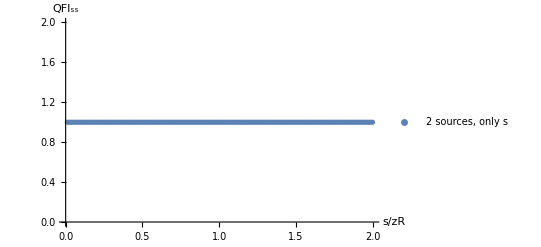

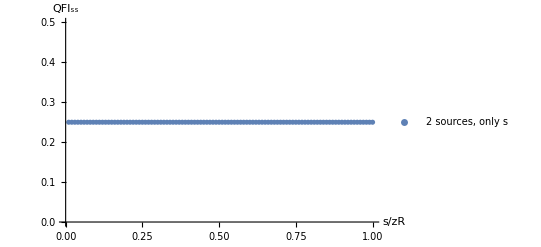

```mathematica
hnum[snum_] := Re[h[[1,1]]]/.{l->snum}
step=0.01;
smax=2;
plot2=Table[hnum[snum],{snum,0.01,smax,step}];
ListPlot[plot2,DataRange->{step,smax},AxesLabel->{"s/zR","QFI_ss"},AxesStyle->14,PlotLegends->{"2 sources, only s"},PlotRange->All]
hnum[pnum_] := Re[h[[2,2]]]/.{p->pnum}
step=0.01;
smax=1;
plot2=Table[hnum[snum],{snum,0.01,smax,step}];
ListPlot[plot2,DataRange->{step,smax},AxesLabel->{"s/zR","QFI_ss"},AxesStyle->14,PlotLegends->{"2 sources, only s"},PlotRange->All]
```